ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

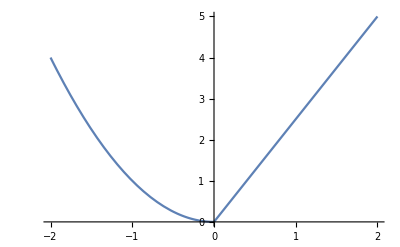

```mathematica
fxn=Piecewise[{
{x^2,x<0},
{x,x>0}
}];
Plot[fxn,{x,-2,2}];

a[t_]:=t^2;

b=ListInterpolation[{0,5},{0,2}][t];

x[t_]=Piecewise[{
{a[t],t<0},
{b,t>0}
}];

Plot[x[t],{t,-2,2}]
```